# Debye-Sears Effect

Calculating the velocity of sound in water.

Jianing  Lu, Jun. 29,  2018

Diffraction phenomenon of light is caused by the density fluctuation in water when ultrasonic waves are passing through it. Variations in water density result in variations of the index of refraction.  A monochromatic light beam travelling perpendicular to the sound wave’s direction will experience diffraction in the same way as if it were passing through a diffraction grating of spacing d = λ1, with its length equal to the wavelength of sound in water.  Using v2 = f2*λ2 for water, and mλ1=dsinθ for the light source, the wavelength of sound in water can be obtained.

## Experimental Data

For a light source with its frequency to be  f = 1.79 ± 0.01 MHz, the pre-obtained data sets of the order m of diffracted lines of and the angle θ  is shown here. Since mλ1=dsinθ, we can see λ1 as the slope when m and dsinθ are x and y, respectively. The measurement error is 0.0083 for all data sets, which is relatively small comparing to the y values, so we don’t have to include error bars in the plot.

Plot the original collected data.

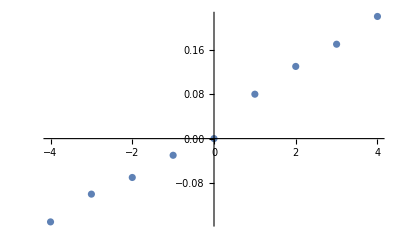

```mathematica
Get["ErrorBarPlots`"]
data={{0,0},{1,0.08},{2,0.13},{3,0.17},{4,0.22},{-1,-0.03},{-2,-0.07},{-3,-0.10},{-4,-0.15}};
errors={.0024,.0024,.0024,.0024,.0024,.0024,.0024,.0024,.0024};
ErrorListPlot[{{{0,0},ErrorBar[0,.0024]},{{1,0.08},ErrorBar[0,.0024]},{{2,0.13},ErrorBar[0,.0024]},{{3,0.17},ErrorBar[0,.0024]},{{4,0.22},ErrorBar[0,.0024]},{{-1,-0.03},ErrorBar[0,.0024]},{{-2,-0.07},ErrorBar[0,.0024]},{{-3,-0.10},ErrorBar[0,.0024]},{{-4,-0.15},ErrorBar[0,.0024]}}]
```

In order to prepare the data for the linear fit, we need to get the data sets of d ∗ sin(θ) vs. m. The spacing d is already measured to be 0.00001016 m. Using the error propagation equation that Δ(sinθ)=(cosθ)⋅Δθ,  the new list of errors is achieved.

Getting the dsinθ values and the errors of them, and plot them vs. m.

0.001016

{0,0.00139626,0.00226893,0.00296706,0.00383972,-0.000523599,-0.00122173,-0.00174533,-0.00261799}

{2.4384×10^-6,2.4384×10^-6,2.43839×10^-6,2.43839×10^-6,2.43838×10^-6,2.4384×10^-6,2.4384×10^-6,2.4384×10^-6,2.43839×10^-6}

{{0,0.},{1,1.4186×10^-6},{2,2.30523×10^-6},{3,3.01453×10^-6},{4,3.90115×10^-6},{-1,-5.31976×10^-7},{-2,-1.24128×10^-6},{-3,-1.77325×10^-6},{-4,-2.65988×10^-6}}

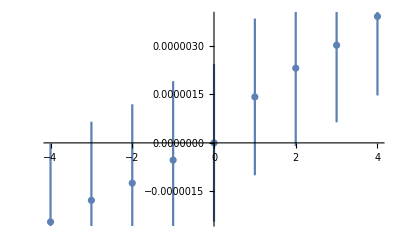

```mathematica
d= 0.001016
k={0,0.08,0.13,0.17,0.22,-0.03,-0.07,-0.10,-0.15}*Pi/180
errors2=d*.0024*Cos[k]
data1=data/.{x_,y_}->{x,d*Sin[y*Pi/180]}
ErrorListPlot[{{{0,0},ErrorBar[0,2.4306012806483072*^-6]},{{1,1.4186031550809047*^-6},ErrorBar[0,2.417824521634139*^-6]},{{2,2.3052288981333136*^-6},ErrorBar[0,2.403249895632273*^-6]},{{3,3.0145282610018936*^-6},ErrorBar[0,2.3796283404477483*^-6]},{{4,3.901150357950497*^-6},ErrorBar[0,2.437302802293531*^-6]},{{-1,-5.319763317004821*^-7},ErrorBar[0,2.437302802293531*^-6]},{{-2,-1.2412778552245132*^-6},ErrorBar[0,2.432428359017597*^-6]},{{-3,-1.7732536197526818*^-6},ErrorBar[0,2.426218156613938*^-6]},{{-4,-2.438391643739713*^-6},ErrorBar[0,2.4110193964392454*^-6]}}]
```

## Linear Curve Fit of mλ1=dsinθ

Next, I’ll apply the linear curve fit function y=ax+b to the prepared data, then the produced slope value is just the wavelength of the light source.

Fit a straight line to the data points.

```mathematica
lm=LinearModelFit[data1,x,x,Weights->1/errors2^2]
```

FittedModel[4.9257×10^-7+8.27518×10^-7 x]

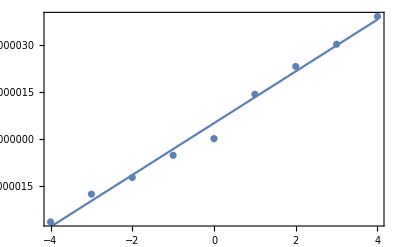

```mathematica
Show[ListPlot[data1],Plot[lm[x],{x,-4,4}],Frame->True]
```

The Wavelength of the light source is just the slope 8.27518×10^-7 m.

## Linear Curve Fit on Wavelength of Sound in Water

Another Curve Fit to eventually get the the velocity of sound in water

8.27518×10^-7

{{0.,0},{8.27518×10^-7,0.00139626},{1.65504×10^-6,0.00226893},{2.48255×10^-6,0.00296706},{3.31007×10^-6,0.00383971},{-8.27518×10^-7,-0.000523599},{-1.65504×10^-6,-0.00122173},{-2.48255×10^-6,-0.00174533},{-3.31007×10^-6,-0.00261799}}

FittedModel[0.000484813+984.252 x]

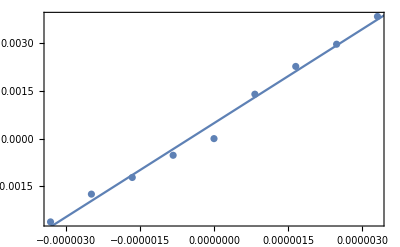

```mathematica
lam= 8.275176281114646*^-7
data2=data/.{x_,y_}->{x*lam,Sin[y*Pi/180]}
lm2=LinearModelFit[data2,x,x,Weights->1/(errors2/d)^2]
Show[ListPlot[data2],Plot[lm2[x],{x,-10,10}],Frame->True]
```

Thus, the wavelength of sound in water is obtained to be 984.252 mm. The velocity is thus 1840 m/s. Comparing with the standard value of 1450 m/s, the error is 0.26. This might be due to the following resons: 1)Water dispersion evidently occurred. 2) Velocity of sound is temperature-dependent, but we were assuming it constant. 3) We were assuming the process to be adiabatic, but in fact, heat exchange between the cell and the air definitely occurred, though it wasn’t a significant factor.

## Author contact information

jianing.lu@mail.utoronto.ca